```mathematica
(***********************************************************)
(***********************************************************)
(*     RoboTerra Bayesian Maximization for snake Fitness           *)
(***********************************************************)
(*
This program is free software:you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation,either version 3 of the License,or
(at your option) any later version. 

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of 
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.See the
GNU General Public License for more details.

You should have received a copy of the GNU General Public License
along with this program.If not,see https://www.gnu.org/licenses/   
*)
(***********************************************************)
(***********************************************************)

Dynamic[HorizontalGauge[pPos,{0,180}]]
```

```mathematica
Dynamic[Length[fitnessHistory]]
```

```mathematica
Dynamic[Show[ListDensityPlot[Append[#⟦1⟧,#⟦2⟧]&/@fitnessHistory,PlotLegends->Automatic],
ListPlot[MapAt[#/.RGBColor[___]->Red&,With[{points=fitnessHistory⟦All,1⟧},
MapIndexed[Style[#,{PointSize[Medium],ColorData["LightTemperatureMap"][
#2⟦1⟧/Length[points]]}]&,points]],-1]]
]
]
```

```mathematica
fitnessHistory={};
```

```mathematica
snakeFitnessRun[4,40]
```

```mathematica
reg = Rectangle[{2,0.2}, {15,1}];
```

Running snakeFitness at {3.1209, 0.50233}

starting position = 138

Fitness was 0.099403677

final pos 27

starting position = 27

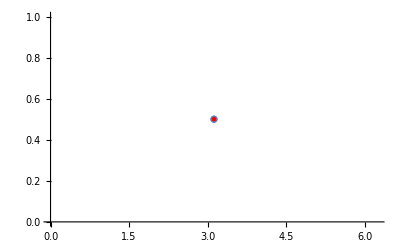
Show[ListDensityPlot[{{3.1209,0.50233,0.099403677}},PlotLegends→Automatic],-Graphics-]

Running snakeFitness at {2.15138, 0.941813}

starting position = 30

Fitness was 1.88314512

final pos 31

starting position = 31

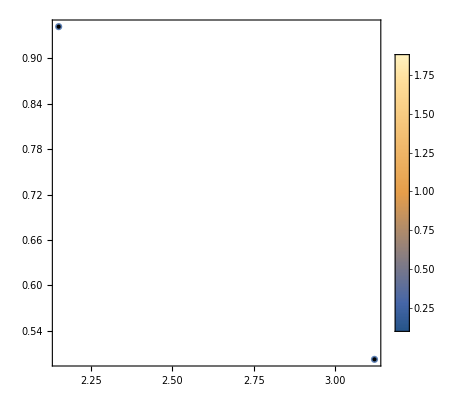

Running snakeFitness at {3.12352, 0.999908}

starting position = 31

Fitness was 3.1739968

final pos 44

starting position = 44

-Graphics-

Running snakeFitness at {13.9411, 0.298092}

starting position = 44

Fitness was 0

final pos 12

starting position = 12

-Graphics-

Running snakeFitness at {2.48944, 0.943633}

starting position = 12

Fitness was 2.84049134

final pos 44

starting position = 44

-Graphics-

Running snakeFitness at {2.85526, 0.923316}

starting position = 44

Fitness was 2.37656794

final pos 40

starting position = 40

-Graphics-

Running snakeFitness at {4.40371, 0.998807}

starting position = 40

Fitness was 3.84251066

final pos 101

starting position = 101

-Graphics-

Running snakeFitness at {10.8132, 0.990895}

starting position = 101

Fitness was 7.2978590

final pos 168

starting position = 168

-Graphics-

Running snakeFitness at {12.0898, 0.901038}

starting position = 168

Fitness was 4.74098409

final pos 116

starting position = 116

-Graphics-

Running snakeFitness at {12.9712, 0.943755}

starting position = 116

Fitness was 5.27974676

final pos 128

starting position = 130

-Graphics-

Running snakeFitness at {10.2492, 0.926001}

starting position = 132

Fitness was 7.2692350

final pos 163

starting position = 163

-Graphics-

Running snakeFitness at {9.56994, 0.913105}

starting position = 163

Fitness was 7.7882552

final pos 170

starting position = 170

-Graphics-

Running snakeFitness at {7.95627, 0.828238}

starting position = 170

Fitness was 7.1722437

final pos 157

starting position = 157

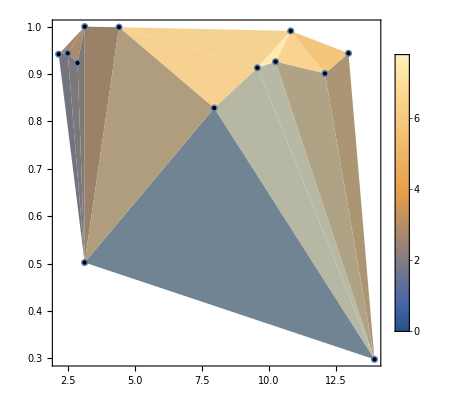

Running snakeFitness at {7.94102, 0.89019}

starting position = 157

Fitness was 7.2792822

final pos 159

starting position = 159

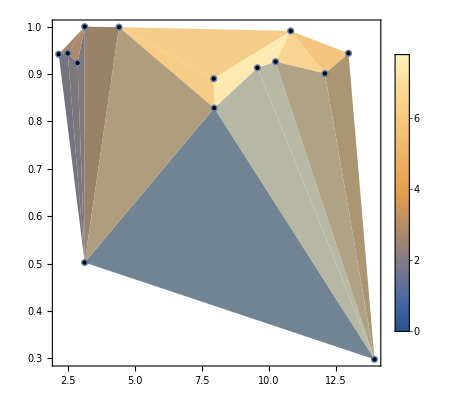

Running snakeFitness at {10.352, 0.747341}

starting position = 165

Fitness was 5.9715509

final pos 136

starting position = 136

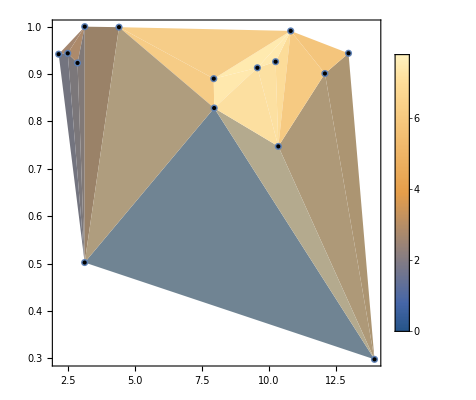

Running snakeFitness at {8.94938, 0.965242}

starting position = 136

Fitness was 8.6879863

final pos 180

starting position = 180

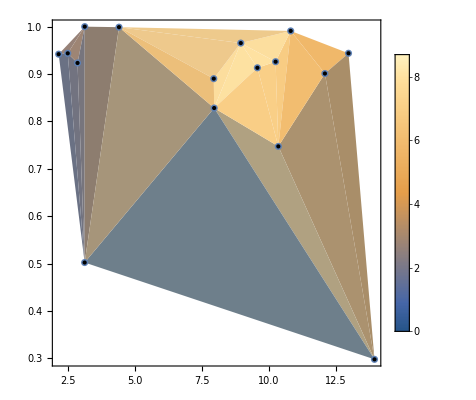

Running snakeFitness at {10.9668, 0.210849}

starting position = 180

Fitness was 0

final pos 13

starting position = 13

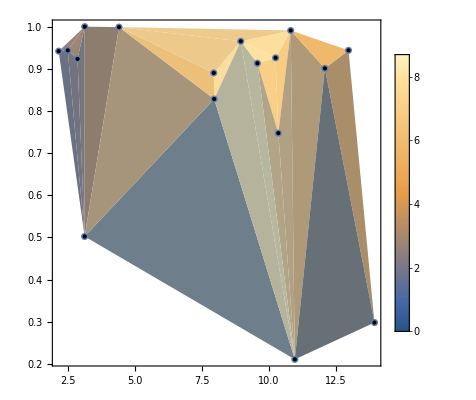

Running snakeFitness at {7.5421, 0.54722}

starting position = 13

Fitness was 3.6620660

final pos 48

starting position = 48

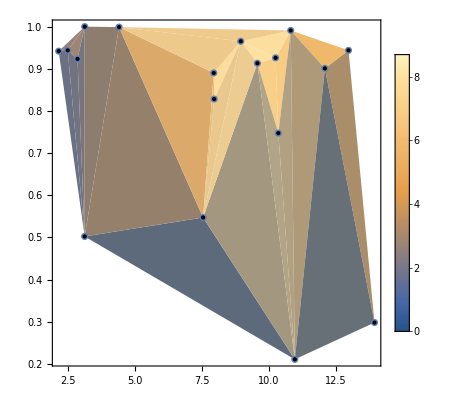

Running snakeFitness at {8.18844, 0.549856}

starting position = 48

Fitness was 4.3934687

final pos 58

starting position = 58

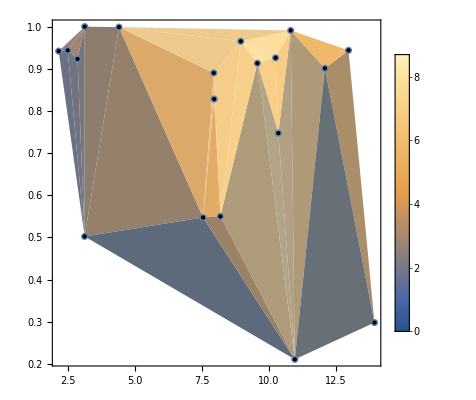

Running snakeFitness at {7.0468, 0.977778}

starting position = 65

Fitness was 6.9958057

final pos 161

starting position = 161

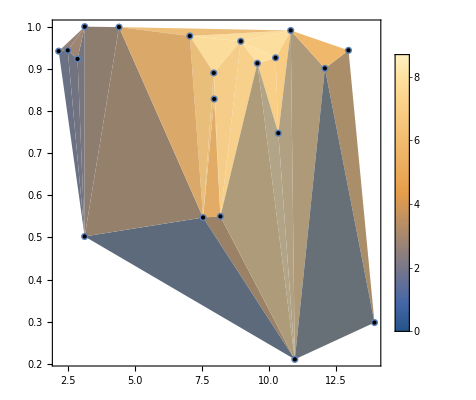

Running snakeFitness at {12.7957, 0.421988}

starting position = 161

Fitness was 0.79430091

final pos 22

starting position = 22

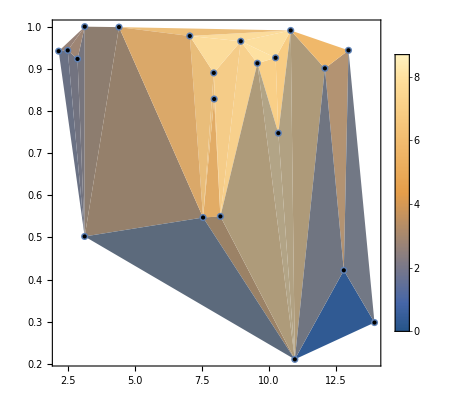

Running snakeFitness at {2.96202, 0.304288}

starting position = 22

Fitness was 3.0629822

final pos 42

starting position = 42

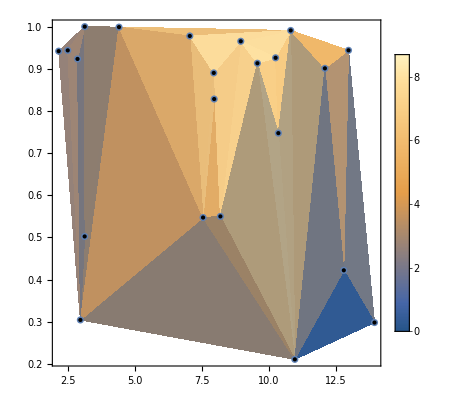

Running snakeFitness at {14.0992, 0.997182}

starting position = 42

Fitness was 3.93031361

final pos 102

starting position = 102

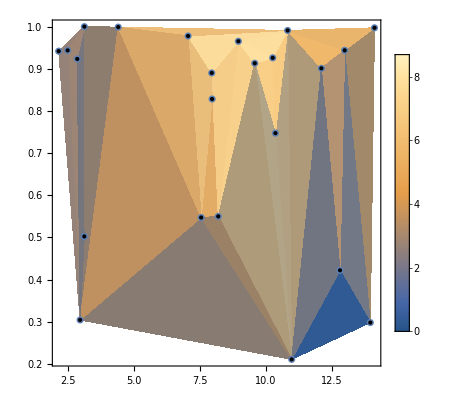

Running snakeFitness at {11.0756, 0.914479}

starting position = 102

Fitness was 6.5150764

final pos 149

starting position = 149

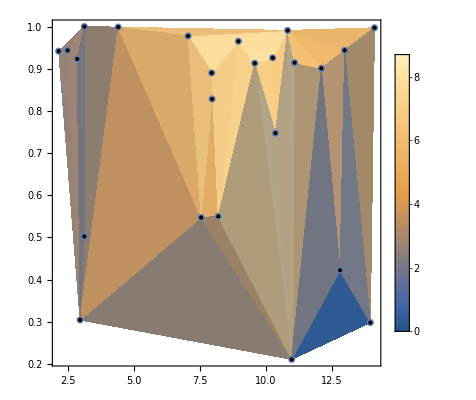

Running snakeFitness at {8.01962, 0.95721}

starting position = 149

Fitness was 7.5600234

final pos 167

starting position = 167

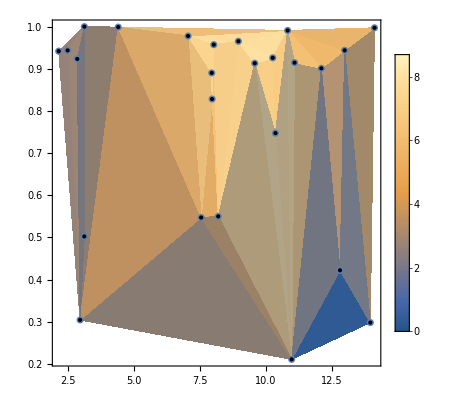

Running snakeFitness at {9.73639, 0.980035}

starting position = 167

Fitness was 7.7250774

final pos 170

starting position = 170

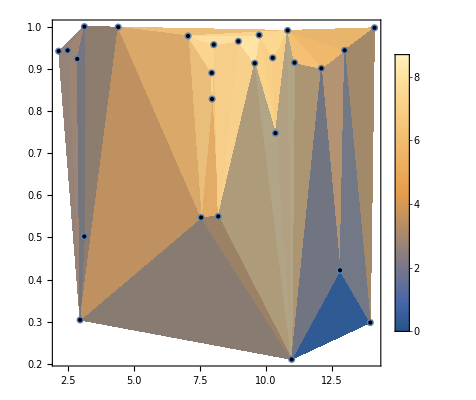

Running snakeFitness at {10.2312, 0.753479}

starting position = 170

Fitness was 5.52915842

final pos 126

starting position = 126

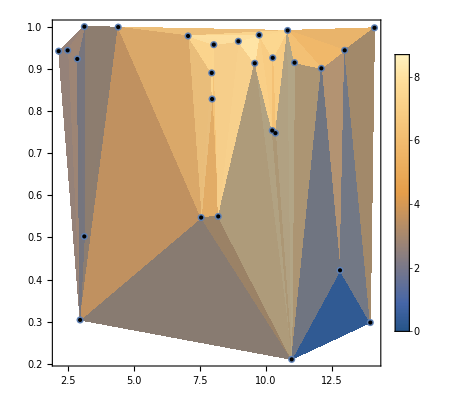

Running snakeFitness at {2.4896, 0.485386}

starting position = 126

Fitness was 0

final pos 26

starting position = 26

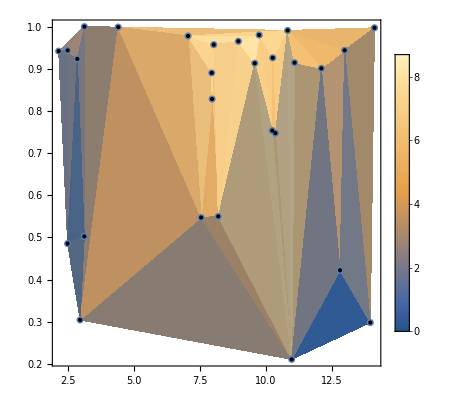

Running snakeFitness at {10.8556, 0.975235}

starting position = 26

Fitness was 5.42968859

final pos 129

starting position = 129

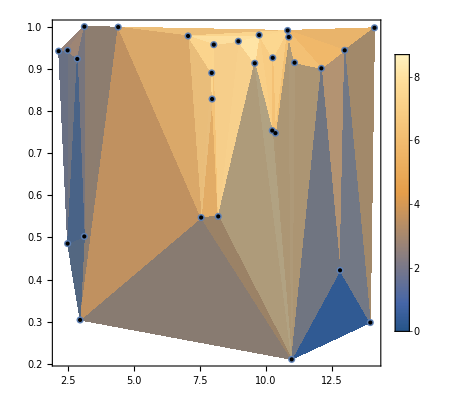

Running snakeFitness at {9.92983, 0.63441}

starting position = 129

Fitness was 4.28063471

final pos 96

starting position = 96

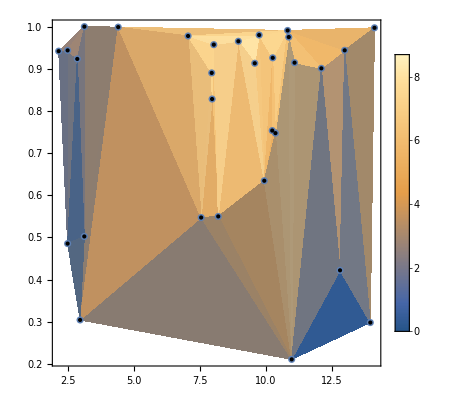

Running snakeFitness at {12.1349, 0.857979}

starting position = 96

Fitness was 5.29545443

final pos 126

starting position = 126

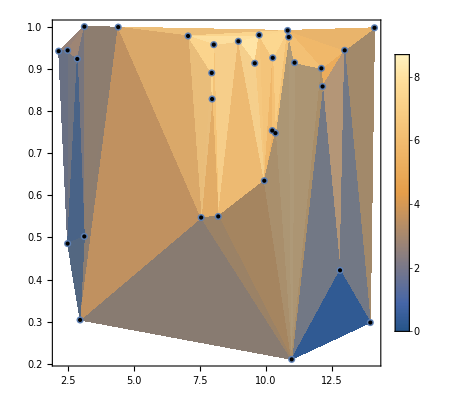

Running snakeFitness at {2.00565, 0.895899}

starting position = 126

Fitness was 2.9930996

final pos 42

starting position = 42

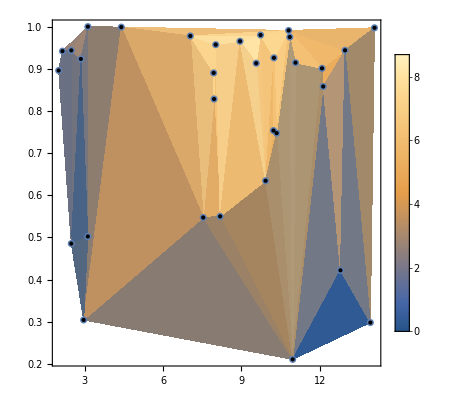

Running snakeFitness at {9.82344, 0.823643}

starting position = 42

Fitness was 6.5909927

final pos 147

starting position = 147

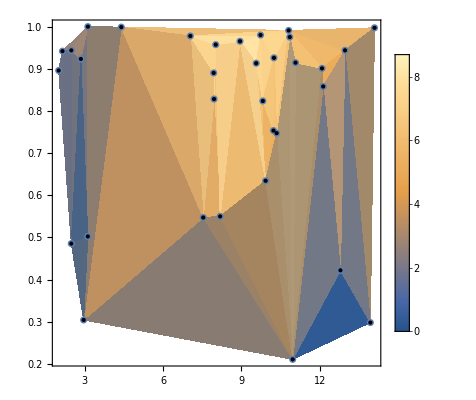

Running snakeFitness at {12.0206, 0.361022}

starting position = 147

Fitness was 0.69769881

final pos 19

starting position = 19

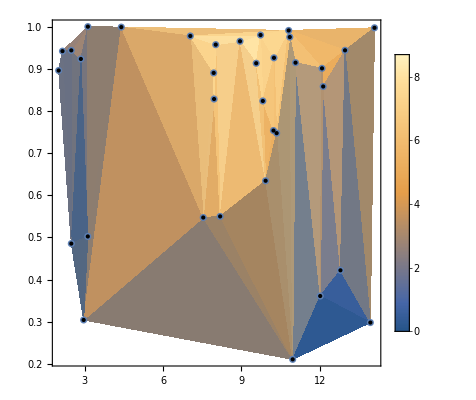

Running snakeFitness at {4.40867, 0.504385}

starting position = 19

Fitness was 0.79552929

final pos 23

starting position = 23

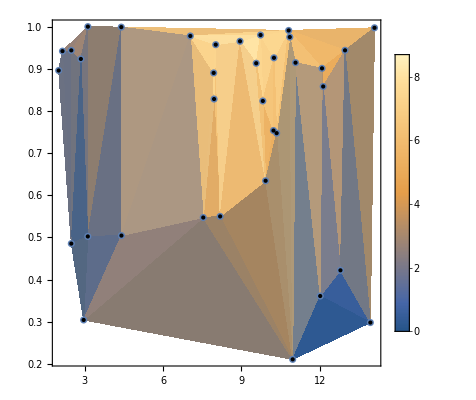

Running snakeFitness at {9.93492, 0.915539}

starting position = 23

Fitness was 7.4855346

final pos 164

starting position = 164

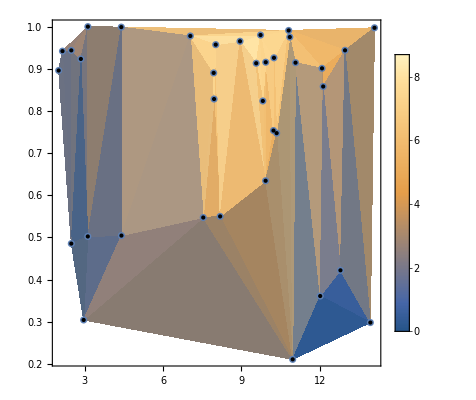

Running snakeFitness at {3.73957, 0.564076}

starting position = 164

Fitness was 1.39520374

final pos 25

starting position = 25

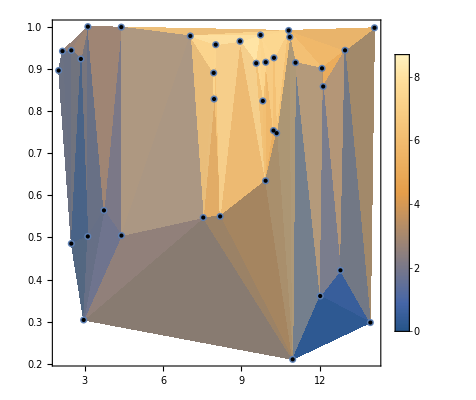

Running snakeFitness at {13.5387, 0.871433}

starting position = 25

Fitness was 4.7733862

final pos 69

starting position = 69

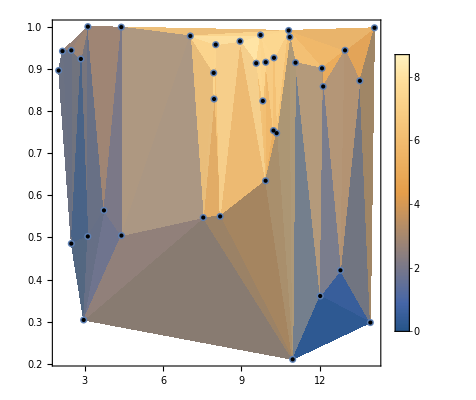

Running snakeFitness at {13.364, 0.320475}

starting position = 69

Fitness was 0

final pos 14

starting position = 14

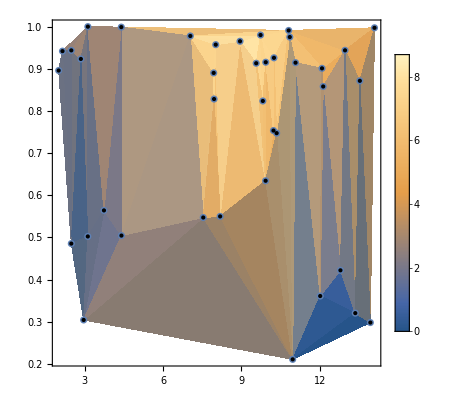

Running snakeFitness at {8.06804, 0.697052}

starting position = 14

Fitness was 5.16449813

final pos 115

starting position = 115

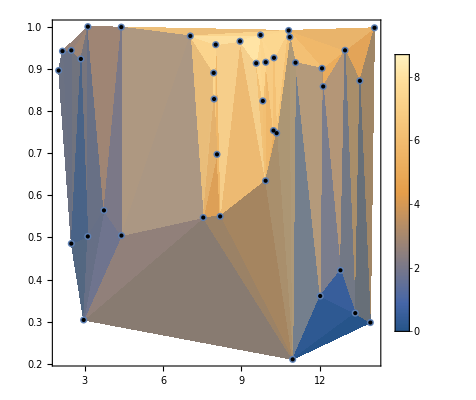

Running snakeFitness at {13.7072, 0.233882}

starting position = 119

Fitness was 0

final pos 23

starting position = 23

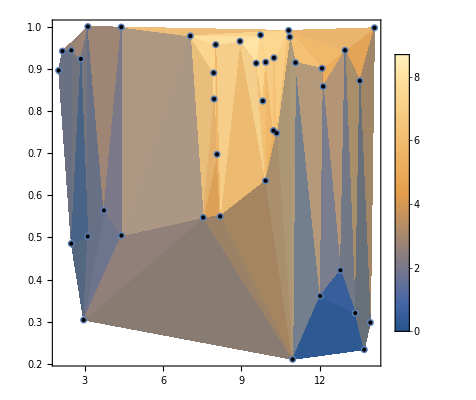

Running snakeFitness at {6.29906, 0.866998}

starting position = 23

Fitness was 6.0963272

final pos 139

starting position = 139

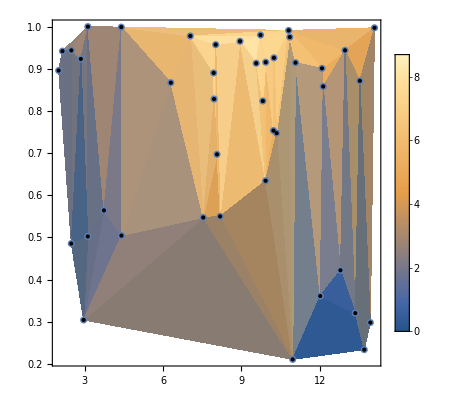

Running snakeFitness at {8.34743, 0.866977}

starting position = 139

Fitness was 7.4910298

final pos 162

starting position = 162

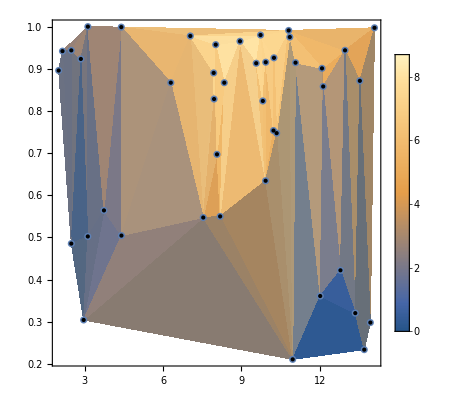

Running snakeFitness at {12.4951, 0.704028}

starting position = 162

Fitness was 5.2853856

final pos 72

starting position = 72

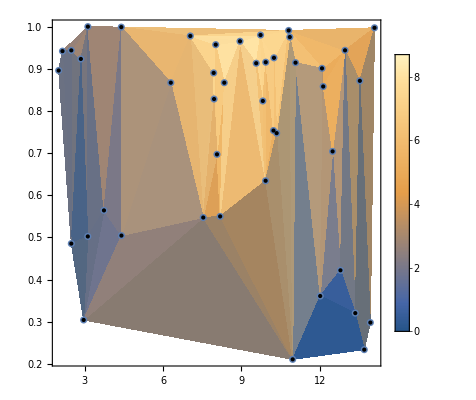

Running snakeFitness at {10.5221, 0.823902}

starting position = 72

Fitness was 6.0959404

final pos 136

starting position = 136

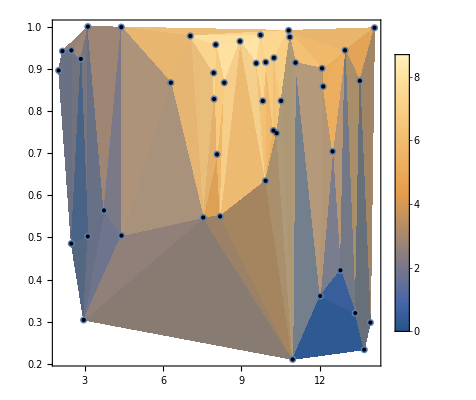

Running snakeFitness at {12.304, 0.208174}

starting position = 136

Fitness was 0

final pos 27

starting position = 27

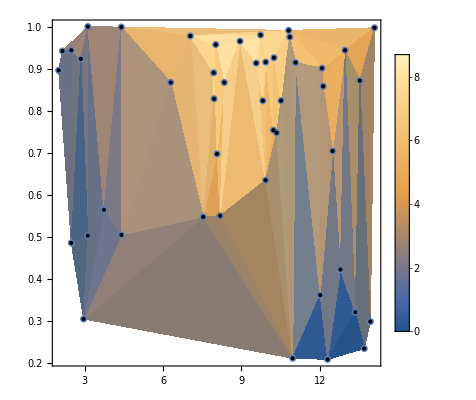

Running snakeFitness at {4.07393, 0.998112}

starting position = 27

Fitness was 4.8716522

final pos 68

starting position = 68

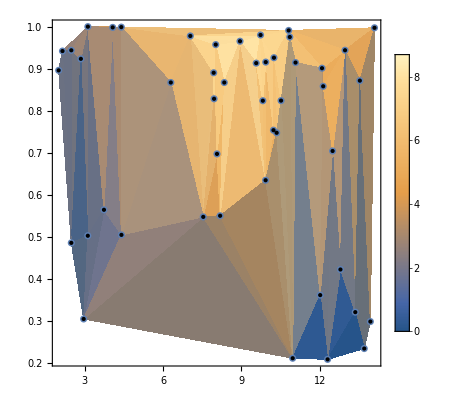

Running snakeFitness at {11.626, 0.646759}

starting position = 68

Fitness was 4.4509043

final pos 63

starting position = 63

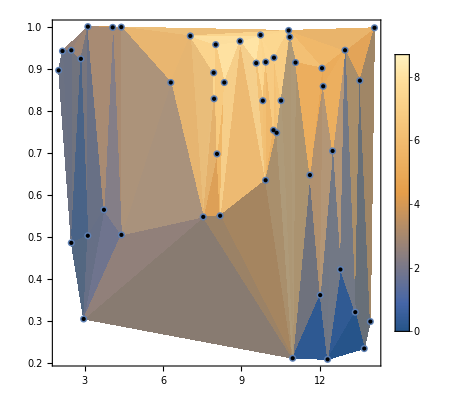

Running snakeFitness at {2.52248, 0.852813}

starting position = 63

Fitness was 1.68728628

final pos 34

starting position = 34

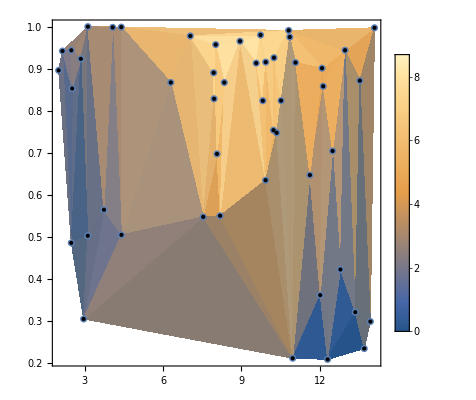

Running snakeFitness at {6.434, 0.953901}

starting position = 34

Fitness was 5.24127197

final pos 125

starting position = 125

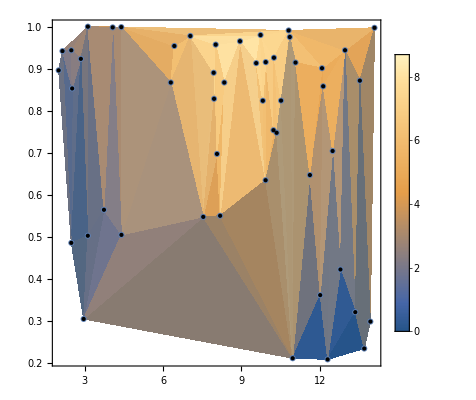

Running snakeFitness at {8.39702, 0.373161}

starting position = 125

Fitness was 2.48287415

final pos 35

starting position = 35

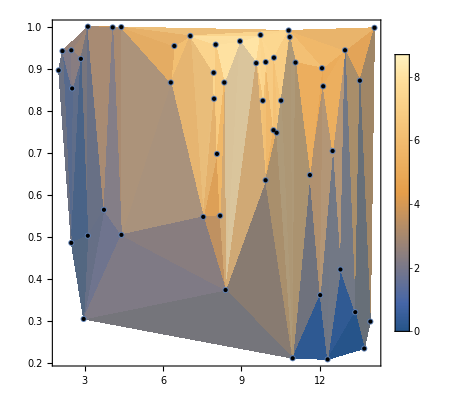

Running snakeFitness at {7.64773, 0.990883}

starting position = 35

Fitness was 7.7720384

final pos 171

starting position = 171

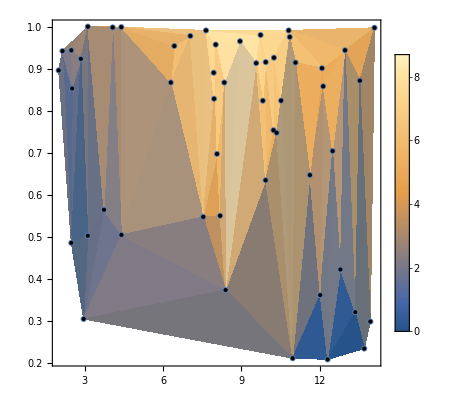

Running snakeFitness at {3.41073, 0.336165}

starting position = 171

Fitness was 0.59789746

final pos 17

starting position = 17

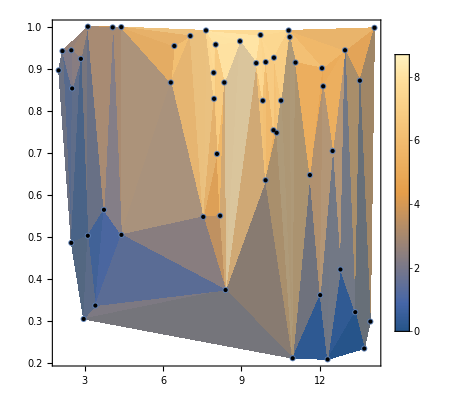

Running snakeFitness at {6.67683, 0.955813}

starting position = 17

Fitness was 6.6654546

final pos 150

starting position = 150

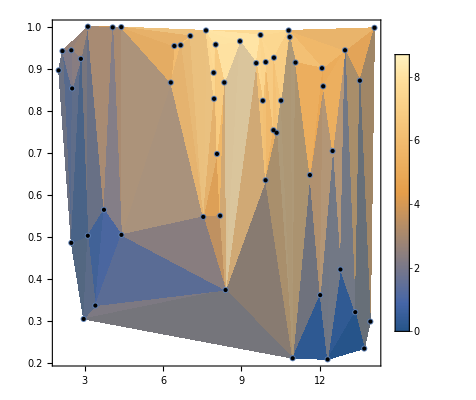

Running snakeFitness at {8.47814, 0.907847}

starting position = 150

Fitness was 7.3722320

final pos 160

starting position = 160

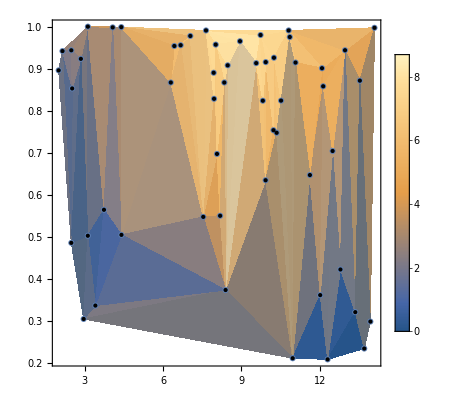

Running snakeFitness at {3.61569, 0.775001}

starting position = 160

Fitness was 2.35595479

final pos 36

starting position = 36

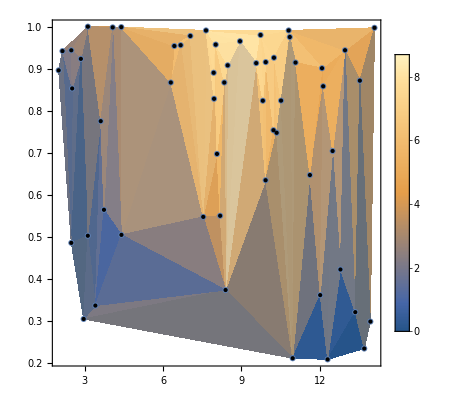

Running snakeFitness at {13.1318, 0.598149}

starting position = 36

Fitness was 1.79998690

final pos 36

starting position = 36

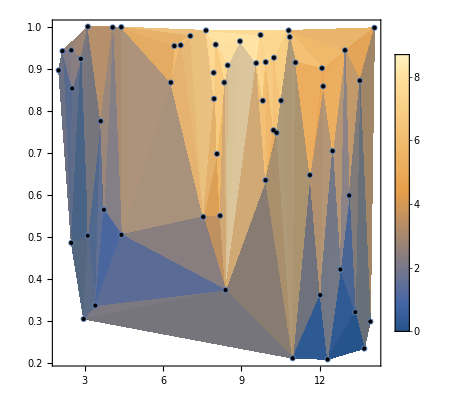

Running snakeFitness at {9.82261, 0.423337}

starting position = 36

Fitness was 2.47890863

final pos 36

starting position = 36

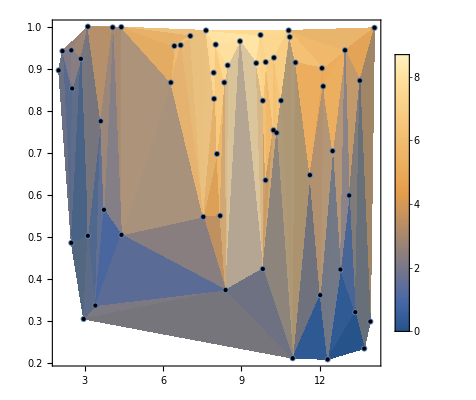

Running snakeFitness at {10.7648, 0.762722}

starting position = 36

Fitness was 5.28721298

final pos 125

starting position = 125

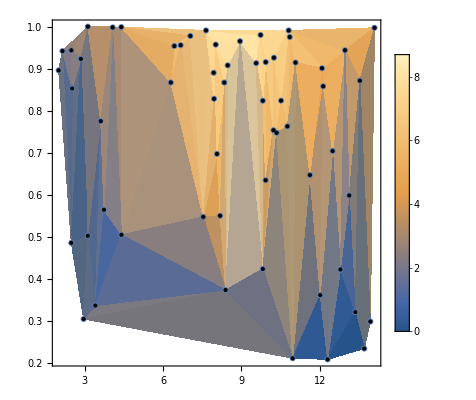

Running snakeFitness at {10.7421, 0.340383}

starting position = 125

Fitness was 0.099607478

final pos 26

starting position = 26

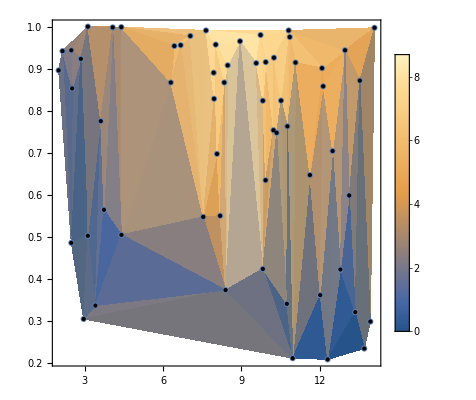

Running snakeFitness at {6.2243, 0.961803}

starting position = 26

Fitness was 6.1898003

final pos 139

starting position = 139

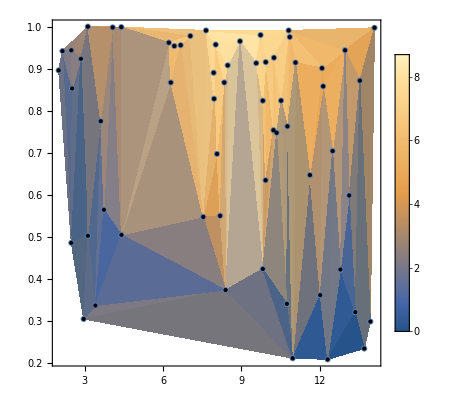

Running snakeFitness at {5.60878, 0.2689}

starting position = 139

Fitness was 0

final pos 12

starting position = 12

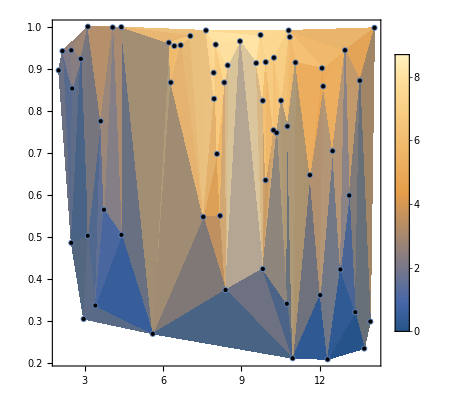

Running snakeFitness at {9.1258, 0.521843}

starting position = 12

Fitness was 4.0972868

final pos 50

starting position = 50

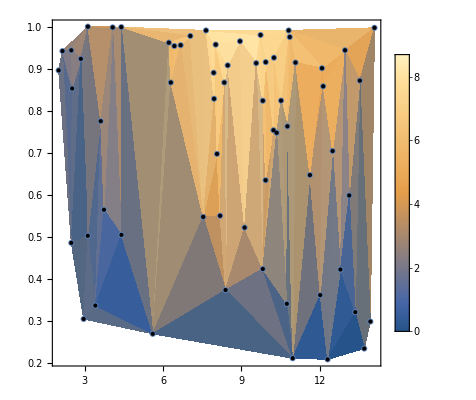

Running snakeFitness at {6.86698, 0.325107}

starting position = 50

Fitness was 0.59899736

final pos 17

starting position = 17

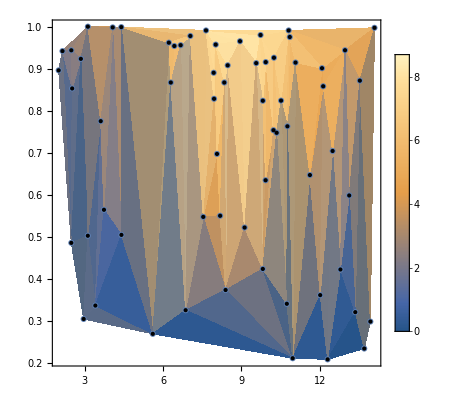

Running snakeFitness at {3.04444, 0.551056}

starting position = 17

Fitness was 1.49347752

final pos 26

starting position = 26

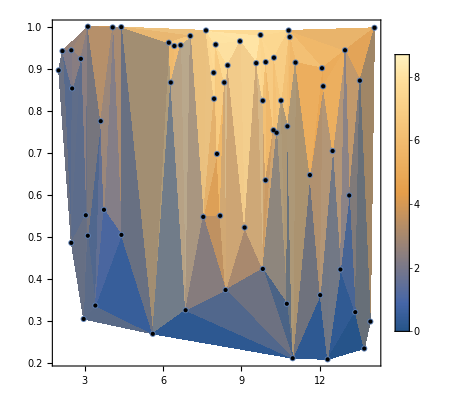

Running snakeFitness at {5.62896, 0.313345}

starting position = 26

Fitness was 1.78729510

final pos 29

starting position = 29

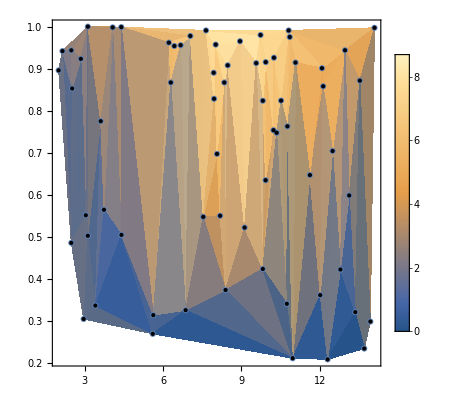

Running snakeFitness at {7.44507, 0.996129}

starting position = 29

Fitness was 5.8908527

final pos 132

starting position = 132

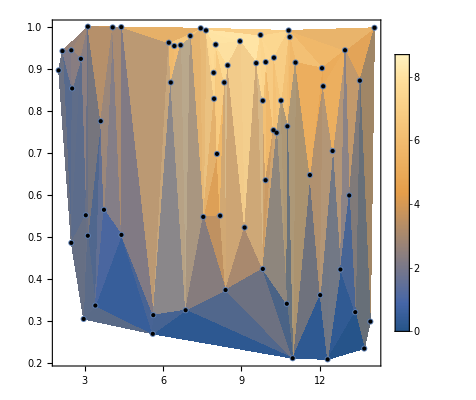

Running snakeFitness at {8.19149, 0.976016}

starting position = 140

Fitness was 8.3333996

final pos 179

starting position = 179

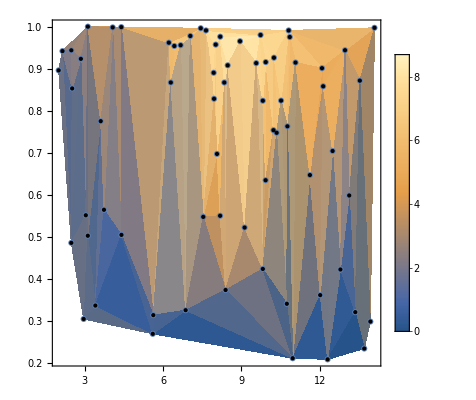

Running snakeFitness at {7.69926, 0.828547}

starting position = 179

Fitness was 6.7841434

final pos 149

starting position = 149

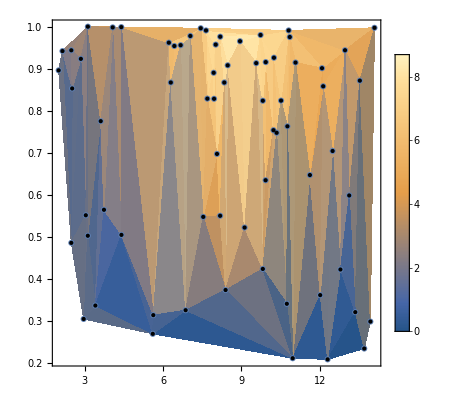

Running snakeFitness at {9.04611, 0.831517}

starting position = 149

Fitness was 7.0796509

final pos 153

starting position = 153

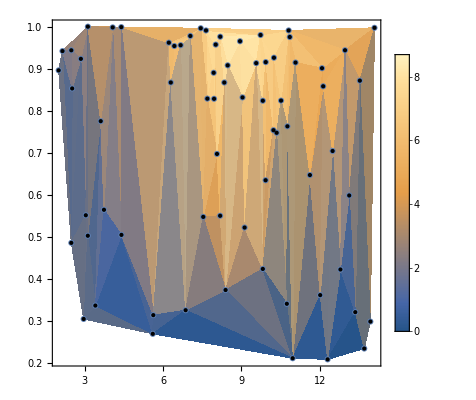

Running snakeFitness at {13.3475, 0.231847}

starting position = 153

Fitness was 0

final pos 13

starting position = 13

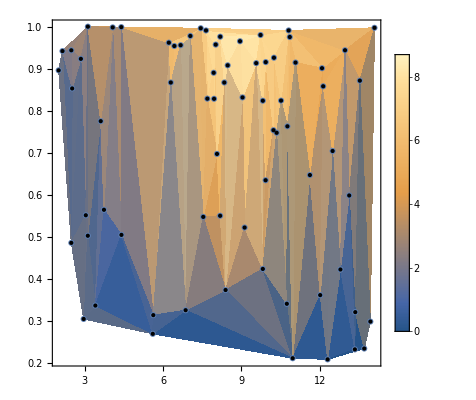

Running snakeFitness at {11.4913, 0.23732}

starting position = 13

Fitness was 0

final pos 10

starting position = 10

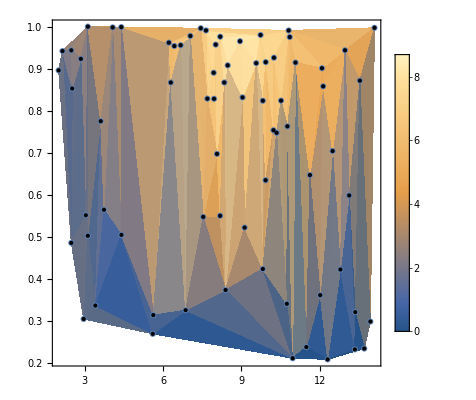

Running snakeFitness at {5.66685, 0.890023}

starting position = 10

Fitness was 4.63531608

final pos 104

starting position = 104

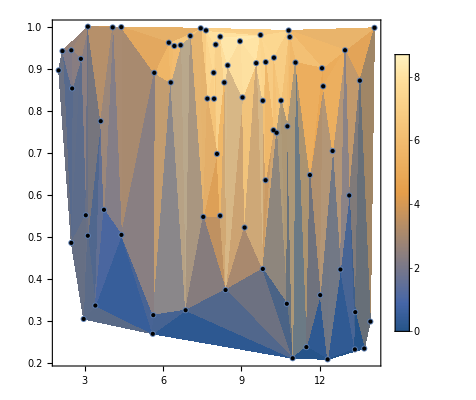

Running snakeFitness at {5.71266, 0.352312}

starting position = 104

Fitness was 0

final pos 23

starting position = 23

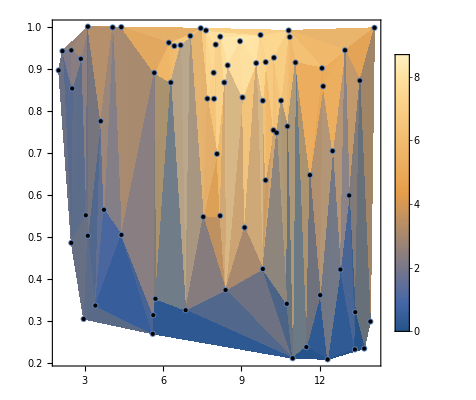

Running snakeFitness at {8.97458, 0.269395}

starting position = 23

Fitness was 0.49785485

final pos 15

starting position = 15

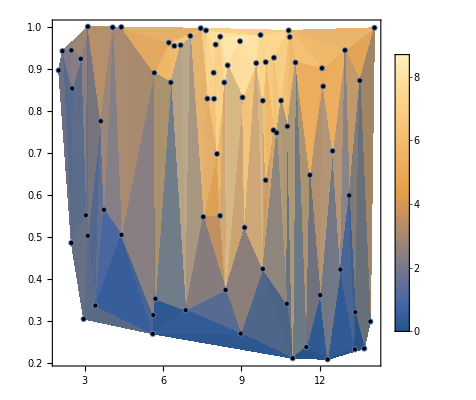

Running snakeFitness at {4.97361, 0.470041}

starting position = 15

Fitness was 0.099730793

final pos 17

starting position = 17

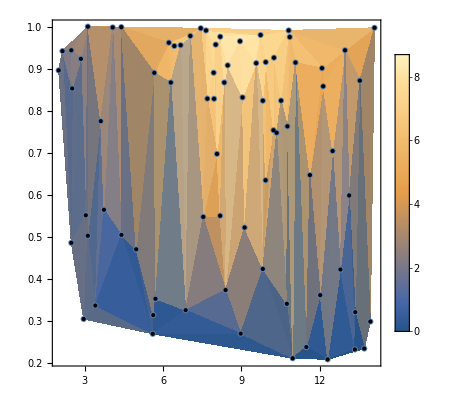

Running snakeFitness at {3.31363, 0.621299}

starting position = 18

Fitness was 0.87367646

final pos 19

starting position = 19

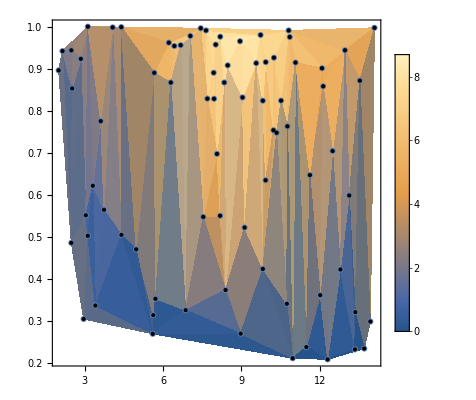

Running snakeFitness at {3.56764, 0.751753}

starting position = 19

Fitness was 2.78828832

final pos 39

starting position = 39

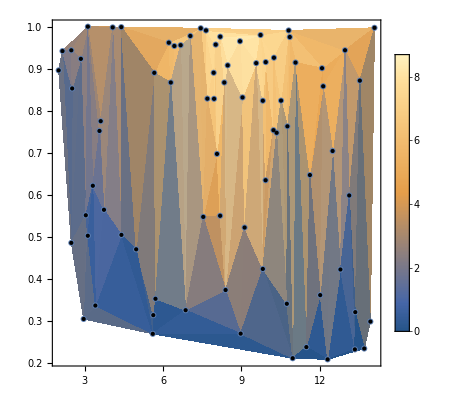

Greater::nord: Invalid comparison with -744.115+3.14159 ⅈ attempted.

Running snakeFitness at {9.33431, 0.252318}

starting position = 39

Fitness was 0

final pos 10

starting position = 10

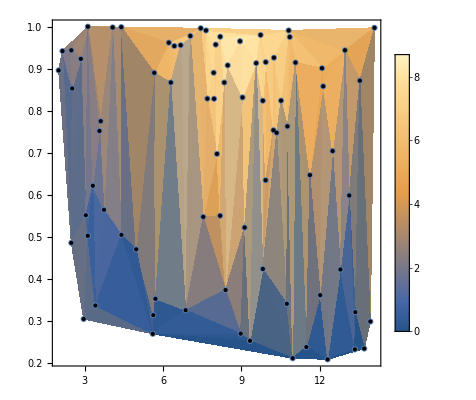

Running snakeFitness at {3.69117, 0.75534}

starting position = 10

Fitness was 2.77426594

final pos 39

starting position = 39

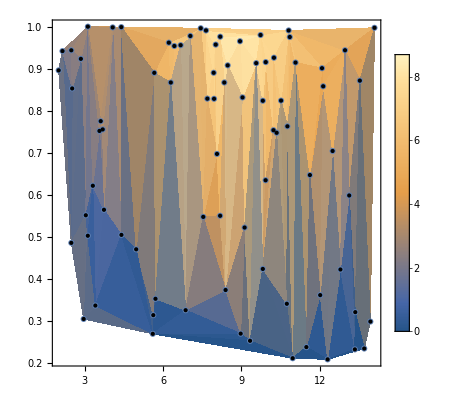

Running snakeFitness at {6.96182, 0.325486}

starting position = 39

Fitness was 0.59980251

final pos 19

starting position = 19

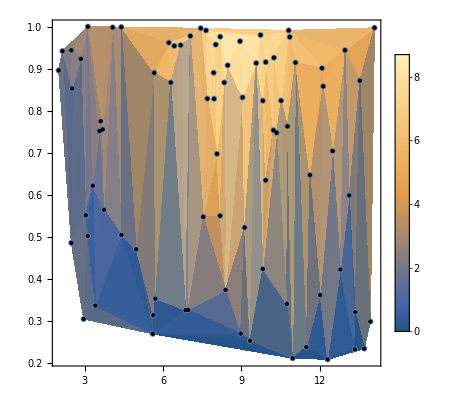

Greater::nord: Invalid comparison with -743.963+3.14159 ⅈ attempted.

Running snakeFitness at {2.32241, 0.92106}

starting position = 19

Fitness was 3.5890730

final pos 50

starting position = 50

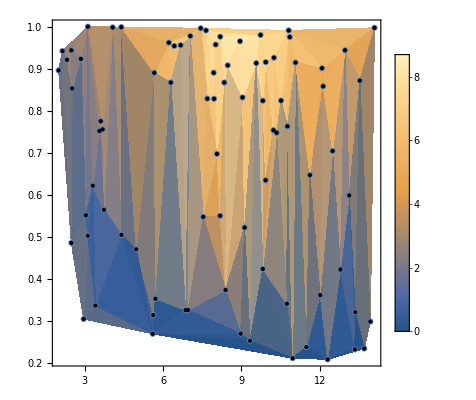

Running snakeFitness at {2.22406, 0.728235}

starting position = 58

Fitness was 0.69902526

final pos 17

starting position = 17

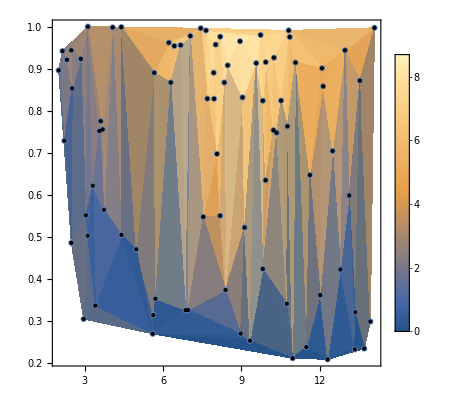

Running snakeFitness at {13.3499, 0.478594}

starting position = 17

Fitness was 0.49546332

final pos 15

starting position = 15

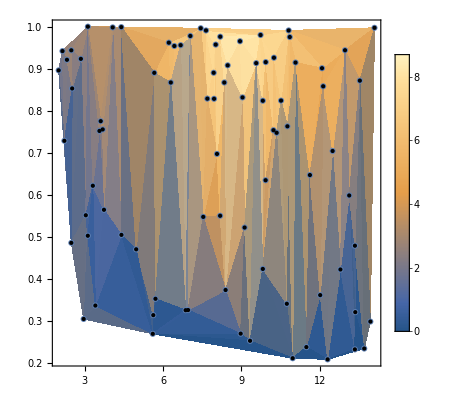

Running snakeFitness at {8.70003, 0.339783}

starting position = 15

Fitness was 0.79394300

final pos 14

starting position = 14

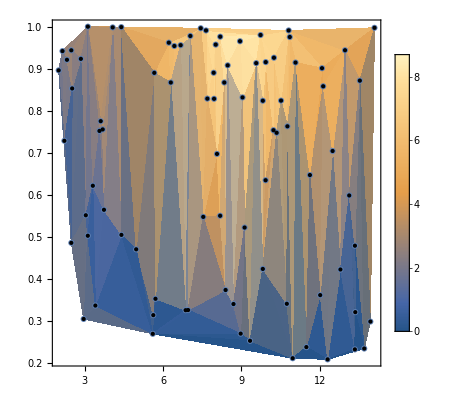

Running snakeFitness at {11.7064, 0.314657}

starting position = 14

Fitness was 2.38434233

final pos 32

starting position = 32

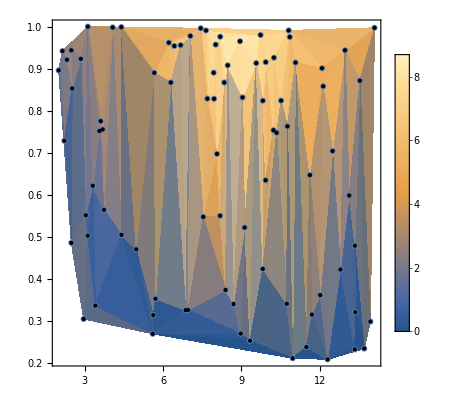

Running snakeFitness at {4.69364, 0.294602}

starting position = 32

Fitness was 0

final pos 6

starting position = 6

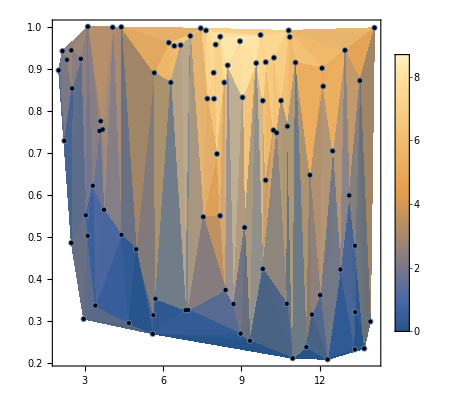

Running snakeFitness at {14.4275, 0.326323}

starting position = 6

Fitness was 0

final pos 7

starting position = 7

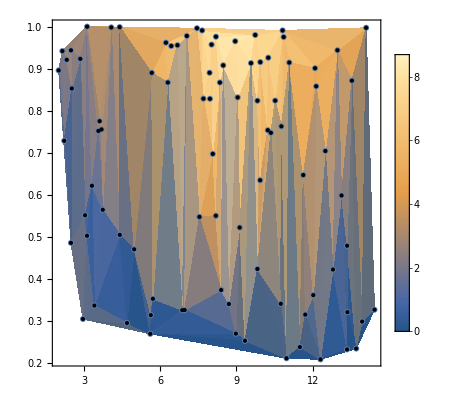

Running snakeFitness at {10.9756, 0.330008}

starting position = 7

Fitness was 0.69618547

final pos 14

starting position = 14

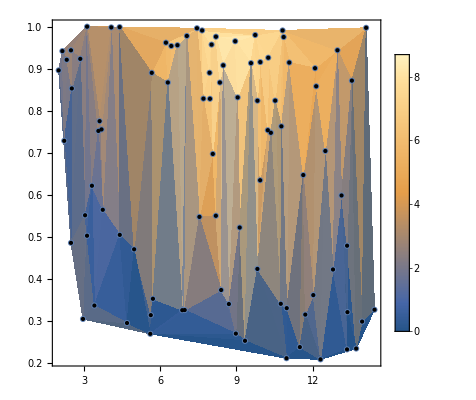

Running snakeFitness at {4.13321, 0.851868}

starting position = 14

Fitness was 3.2743497

final pos 49

starting position = 49

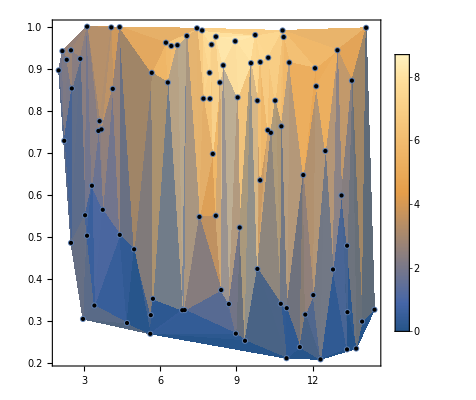

Running snakeFitness at {5.87856, 0.502146}

starting position = 49

Fitness was 1.09147410

final pos 27

starting position = 27

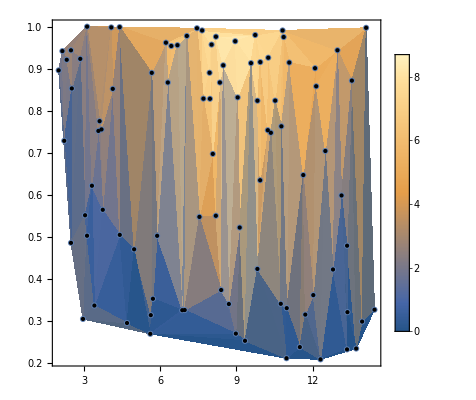

Running snakeFitness at {13.8504, 0.254463}

starting position = 27

Fitness was 0

final pos 10

starting position = 10

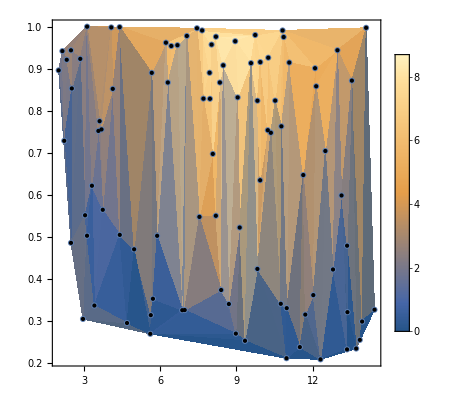

Running snakeFitness at {3.07371, 0.362279}

starting position = 10

Fitness was 0

final pos 9

starting position = 9

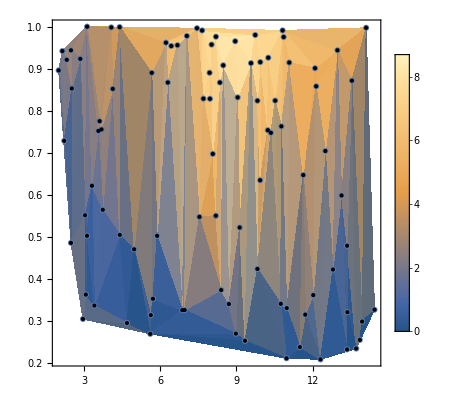

Running snakeFitness at {4.84151, 0.256781}

starting position = 9

Fitness was 0

final pos 9

starting position = 9

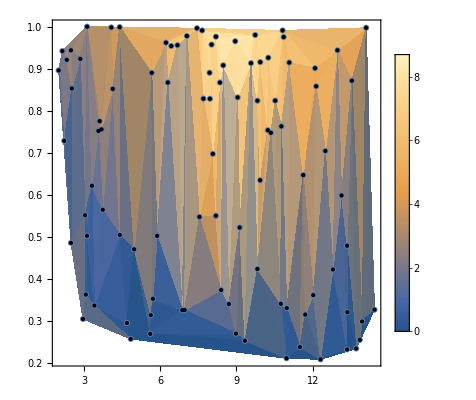

Running snakeFitness at {12.8226, 0.35261}

starting position = 9

Fitness was 0

final pos 10

starting position = 10

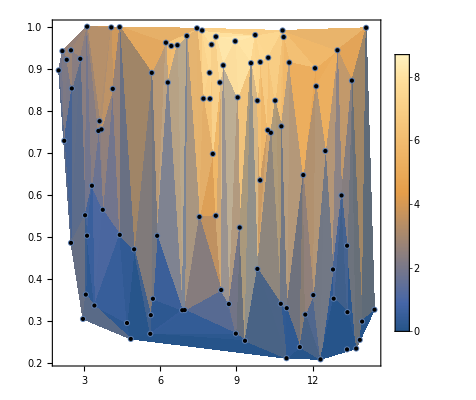

Running snakeFitness at {5.18102, 0.374284}

starting position = 10

Fitness was 0

final pos 11

starting position = 11

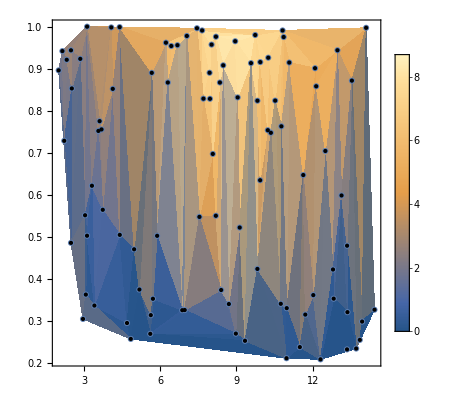

Running snakeFitness at {4.12647, 0.812545}

starting position = 11

Fitness was 2.8722940

final pos 44

starting position = 44

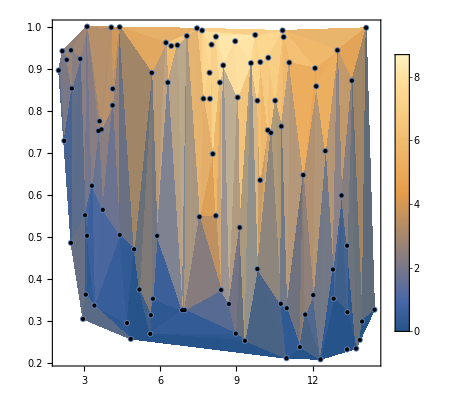

Running snakeFitness at {2.13426, 0.429768}

starting position = 44

Fitness was 0

final pos 13

starting position = 13

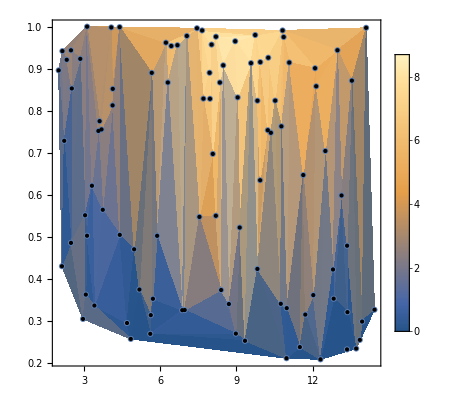

Running snakeFitness at {14.7468, 0.295605}

starting position = 13

Fitness was 0

final pos 8

starting position = 8

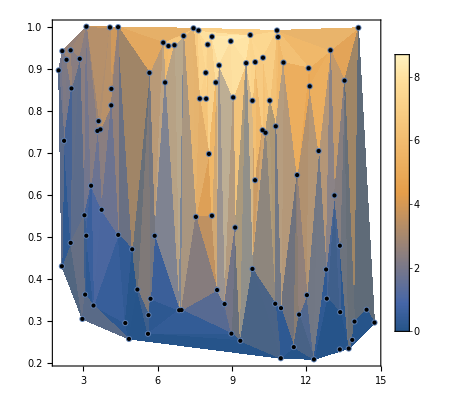

Running snakeFitness at {9.7367, 0.226286}

starting position = 8

Fitness was 0

final pos 8

starting position = 8

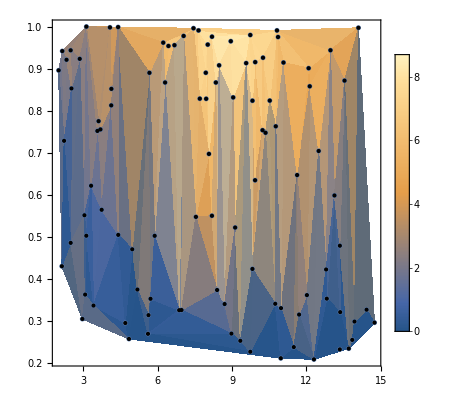

BayesianMaximizationObject[…]

```mathematica
bo= BayesianMaximization[snakeFitnessRun@@#&,reg, MaxIterations-> 100]
```

```mathematica
bo= BayesianMaximization[snakeFitnessRun@@#&,reg, MaxIterations-> 100,InitialEvaluationHistory->Dataset[<|"Configuration"->#1,"Value"->#2|>&@@@fitnessHistory]]
```

```mathematica
LaunchKernels[1];
```

```mathematica
(*LocalSubmit[plotNicePicture[fitnessHistory]];*)
```

```mathematica
plotNicePicture[fitnessHistory];
```

```mathematica
bo
```

BayesianMaximizationObject[…]

Running snakeFitness at {8.95, 0.965}

starting position = 8

Fitness was 7.7275013

final pos 165

starting position = 165

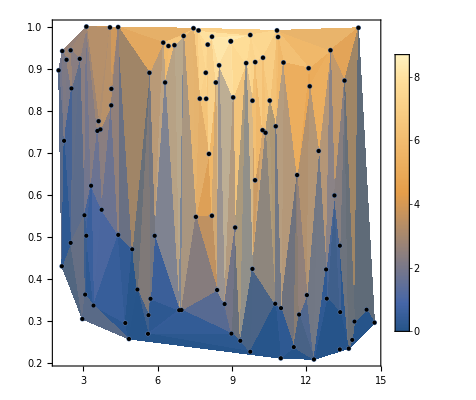

7.7275013

```mathematica
snakeFitnessRun[8.95,0.965]
```

```mathematica
Export["fitnessHistory.dat",fitnessHistory]
```

fitnessHistory.dat